# PHY 362 K Homework 5

Problem 1

### (a)

```mathematica
m:=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ℏ^2/2, 0, 0, 0, 0, 0}, {0, 0, 0, -ℏ^2/2, ℏ^2/(√2), 0, 0, 0}, {0, 0, 0, ℏ^2/(√2), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ℏ^2/(√2), 0}, {0, 0, 0, 0, 0, ℏ^2/(√2), -ℏ^2/2, 0}, {0, 0, 0, 0, 0, 0, 0, ℏ^2/2}})
```

```mathematica
eigen:=Eigensystem[m]
values:=Part[eigen,1]
vectors:=Part[eigen,2]
Do[Print[TeXForm[Part[values,i]]],{i,1,8}]
Do[Print[TeXForm[Normalize[Part[vectors,i]]//MatrixForm]],{i,1,8}]
```

-\hbar ^2

-\hbar ^2

\frac{\hbar ^2}{2}

\frac{\hbar ^2}{2}

\frac{\hbar ^2}{2}

«1 more identical outputs»

0

0

\left(
\begin{array}{c}
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 -\frac{1}{\sqrt{3}} \\
 \sqrt{\frac{2}{3}} \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 0 \\
 0 \\
 -\sqrt{\frac{2}{3}} \\
 \frac{1}{\sqrt{3}} \\
 0 \\
 0 \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 1 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 \sqrt{\frac{2}{3}} \\
 \frac{1}{\sqrt{3}} \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 0 \\
 0 \\
 \frac{1}{\sqrt{3}} \\
 \sqrt{\frac{2}{3}} \\
 0 \\
 0 \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 0 \\
 1 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 0 \\
 1 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
\end{array}
\right)

\left(
\begin{array}{c}
 1 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
 0 \\
\end{array}
\right)

Problem 2

### (b)

```mathematica
ReleaseHold[H']
H':={{-(11*a^2*En)/48, (a^2*En)/(6*Sqrt[2])},{(a^2*En)/(6*Sqrt[2]), -(7*a^2*En)/48}}
JordanDecomposition[H']
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[H']

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

SetDelayed::write: Tag Hold in SuperscriptBox[ is Protected.

$Failed

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[H']

```mathematica
Eigensystem[H']
```

{{-(5 a^2 En)/16,-(a^2 En)/16},{{-√2,1},{1/(√2),1}}}

### (c)

```mathematica
Simplify[Norm[H',"Frobenius"],a∈Reals&&a>0&&En∈Reals&&En>0]
```

1/8 √(13/2) a^2 En

```mathematica
Hz:={{0,0},{0,-mu*B}}
```

```mathematica
Norm[Hz,"Frobenius"]
```

Abs[B mu]

```mathematica
En:=(13.6/4)*1.6*10^(-19)
a:=7.2974*10^(-3)
mu:=9.273*10^(-24)
Simplify[Solve[mu*B==1/8 √(13/2) a^2 En,B],B∈Reals&&B>0]
```

{{B→0.995593}}

### (d)

```mathematica
Clear[En]
Clear[a]
Clear[mu]
H:={{-(11*a^2*En)/48, (a^2*En)/(6*Sqrt[2])},{(a^2*En)/(6*Sqrt[2]), -(7*a^2*En)/48- mu*B}}
```

```mathematica
JordanDecomposition[H]
f:=1/48 (-9 a^2 En-24 B mu-2 √3 √(3 a^4 En^2-8 a^2 B En mu+48 B^2 mu^2))
g:=1/48 (-9 a^2 En-24 B mu+2 √3 √(3 a^4 En^2-8 a^2 B En mu+48 B^2 mu^2))
```

JordanDecomposition[{{-6.63876×10^-24,3.41404×10^-24},{3.41404×10^-24,-4.22466×10^-24-9.273×10^-24 B}}]

```mathematica
En:=(13.6/4)*1.6*10^(-19)
a:=7.2974*10^(-3)
mu:=9.273*10^(-24)
Plot[{f,g},{B,0,5*0.995592544948975},PlotLabel->"Eigenvalues as function of B",AxesLabel->{"B","H'"},PlotLegends->{"f(B)","g(B)"}]
```

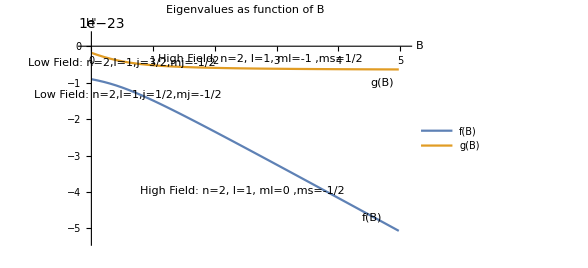

### (e)

```mathematica
Clear[f']
Clear[g']
B:=20*0.995592544948975
```

```mathematica
f
```

-1.88931×10^-22

```mathematica
g
```

-6.57482×10^-24

```mathematica
B
```

19.9119

```mathematica
g':=mu*B*(-1+2*1/2)
```

```mathematica
g'
```

0.

```mathematica
f':=mu*B*(0-2*1/2)
```

```mathematica
f'
```

-1.84643×10^-22

```mathematica
0
```

### (f)

```mathematica
Clear[En]
Clear[a]
Clear[mu]
Clear[B]
Simplify[Series[f,{B,0,1}],En∈Reals&&a∈Reals&&mu∈Reals&&En>0]
```

-5/16 (a^2 En)-(mu B)/3+O[B]^2

```mathematica
Simplify[Series[g,{B,0,1}],En∈Reals&&a∈Reals&&mu∈Reals&&En>0]
```

-(a^2 En)/16-(2 mu B)/3+O[B]^2

Problem 3

### (a)

```mathematica
U[n_,l_,m_,r_,t_,phi_]:=Sqrt[(2/(n a))^3 ((n-l-1)!/(2 n (n+l)!))]*Exp[-r/(n a)]*(2 r/(n a))^l*LaguerreL[n-l-1,2 l+1,2 r/(n a)]*SphericalHarmonicY[l,m,t,phi]
```

```mathematica
Simplify[Integrate[Conjugate[U[2,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

(128 √2 a)/243

```mathematica
Simplify[Integrate[Conjugate[U[3,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

(27 a)/(64 √2)

```mathematica
Simplify[Integrate[Conjugate[U[4,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

(6144 a)/(15625 √5)

```mathematica
DeltaE[n_]:=(-13.6+(13.6/n^2))
DeltaE[2]
DeltaE[3]
DeltaE[4]
```

-10.2

-12.0889

-12.75

```mathematica
V:=80000
```

```mathematica
a:=0.529*10^(-10)
```

```mathematica
(V*Out[49])/Out[61]
```

-3.09075×10^-7

```mathematica
(V*Out[50])/Out[62]
```

-1.04431×10^-7

```mathematica
(V*Out[51])/Out[63]
```

-5.83689×10^-8

```mathematica
Clear[V]
Clear[a]
Energy[n_]:=-2*(fourpi)*ep*a*V^2*((Simplify[Integrate[Conjugate[U[n,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]^2)/(1-(1/n^2)))
```

```mathematica
Energy[2]+Energy[3]+Energy[4]
```

-(61859983260077542739 a^3 ep fourpi V^2)/35429400000000000000

```mathematica
Energy[3]
```

-1.17927×10^-21 V^2 Abs[a]^2

```mathematica
61859983260077542739/35429400000000000000
```

61859983260077542739/35429400000000000000

```mathematica
N[61859983260077542739/35429400000000000000]
```

1.74601

Problem 4

### (c)

```mathematica
a:=0.529*10^(-10)
10^(-7)*(8*Pi)/3*9.273*10^(-24)*2*0.8574*5.0507*10^(-27)*1/(Pi*a^3)*(1/2)*((3/2) * (5/2)- (1/2) * (3/2)-2)
```

7.23364×10^-26

```mathematica
%/(6.63*10^(-34))
```

1.09105×10^8